```mathematica
ClearAll["Global`*"];

(*Pixel size from the raw 100 nm bead TIFF metadata.*)
pixelSizeUm=0.0906000048742803;

beadStackPath=SystemDialogInput["FileOpen",WindowTitle->"Select 100 nm bead TIFF stack"];

channelNumber=3;
zSliceNumber=11;
projectionMethod="Sum";

(*Convert imported numeric arrays into grayscale matrices.*)
toGrayMatrix[array_]:=Module[{dims=Dimensions[array]},Which[MatrixQ[array,NumericQ],N[array],ArrayDepth[array]==3&&MemberQ[{3,4},Last[dims]],N@Map[Mean,array[[All,All,1;;Min[3,Last[dims]]]],{2}],True,$Failed]];

(*Convert TIFF raw data into a list of 2D frames.*)
extractFrames[data_]:=Module[{depth},depth=ArrayDepth[data];
Which[Head[data]===Image,{ImageData[data]},ListQ[data]&&AllTrue[data,Head[#]===Image&],ImageData/@data,MatrixQ[data,NumericQ],{N[data]},depth==3&&MemberQ[{3,4},Last[Dimensions[data]]],{toGrayMatrix[data]},depth==3,N/@data,depth==4,DeleteCases[toGrayMatrix/@data,$Failed],True,{}]];

(*Read raw intensity data,not display-normalized ImageJ composite images.*)
rawData=Quiet@Check[Import[beadStackPath,"Data"],$Failed];

rawFrames=If[rawData===$Failed,{},extractFrames[rawData]];

If[rawFrames==={},rawFrames=ImageData/@Import[beadStackPath,"ImageList"];];

rawFrames=N/@rawFrames;

(*ImageJ hyperstack order is assumed to be:z1 ch1,z1 ch2,z1 ch3,z2 ch1,z2 ch2,z2 ch3,...*)
channelFrames[channelIndex_]:=rawFrames[[channelIndex;; ;;channelNumber]];

(*Sum projection across z-slices for each channel.*)
projectFrames[frames_]:=Total[frames];

channelProjectionData=Table[projectFrames[channelFrames[ch]],{ch,1,channelNumber}];

channelProjectionImages=ImageAdjust[Image[#,"Real"]]&/@channelProjectionData;

fitProjectedBeadPsf[data_,channelIndex_,roiRadius_:10,searchRadius_:80]:=Module[{h,w,centerY,centerX,ySearch,xSearch,searchData,localPeak,peakY,peakX,yRange,xRange,roiData,borderPixels,background,amplitude,fitData,model,fit,roiHeight,roiWidth,bValue,fwhmPixels,fittedData,residual,totalVariance,r2},If[!MatrixQ[data,NumericQ],Return[<|"Channel"->channelIndex,"psfCoefficient"->Missing["InvalidData"]|>]];
{h,w}=Dimensions[data];
centerY=Round[h/2];
centerX=Round[w/2];
ySearch=Range[Max[1,centerY-searchRadius],Min[h,centerY+searchRadius]];
xSearch=Range[Max[1,centerX-searchRadius],Min[w,centerX+searchRadius]];
searchData=data[[ySearch,xSearch]];
localPeak=First@Position[searchData,Max[searchData]];
peakY=ySearch[[localPeak[[1]]]];
peakX=xSearch[[localPeak[[2]]]];
yRange=Range[Max[1,peakY-roiRadius],Min[h,peakY+roiRadius]];
xRange=Range[Max[1,peakX-roiRadius],Min[w,peakX+roiRadius]];
roiData=N@data[[yRange,xRange]];
{roiHeight,roiWidth}=Dimensions[roiData];
borderPixels=Join[roiData[[1]],roiData[[-1]],roiData[[All,1]],roiData[[All,-1]]];
background=Median[borderPixels];
amplitude=Max[roiData]-background;
If[!NumericQ[amplitude]||amplitude<=0,Return[<|"Channel"->channelIndex,"Peak X"->peakX,"Peak Y"->peakY,"Peak intensity"->Max[roiData],"Background"->background,"Peak minus background"->amplitude,"psfCoefficient"->Missing["NoSignal"],"FWHM pixels"->Missing["NoSignal"],"FWHM nm"->Missing["NoSignal"],"R2"->Missing["NoSignal"],"Projection image"->ImageAdjust[Image[data,"Real"]],"ROI image"->ImageAdjust[Image[roiData,"Real"]]|>]];
fitData=Flatten[Table[{x,y,roiData[[y,x]]},{y,1,roiHeight},{x,1,roiWidth}],1];
model=a Exp[-b ((x-x0)^2+(y-y0)^2)]+c;
(*Bounds prevent unstable fits;Quiet suppresses harmless Gaussian-tail underflow if the optimizer tests extremely small values.*)fit=Quiet[Check[FindFit[fitData,{model,a>0&&0.01<b<1.2&&1<=x0<=roiWidth&&1<=y0<=roiHeight},{{a,amplitude},{b,0.44},{c,background},{x0,(roiWidth+1)/2},{y0,(roiHeight+1)/2}},{x,y},MaxIterations->1000],$Failed],General::munfl];
If[fit===$Failed||!NumericQ[b/. fit]||(b/. fit)<=0,Return[<|"Channel"->channelIndex,"Peak X"->peakX,"Peak Y"->peakY,"Peak intensity"->Max[roiData],"Background"->background,"Peak minus background"->amplitude,"psfCoefficient"->Missing["FitFailed"],"FWHM pixels"->Missing["FitFailed"],"FWHM nm"->Missing["FitFailed"],"R2"->Missing["FitFailed"],"Projection image"->ImageAdjust[Image[data,"Real"]],"ROI image"->ImageAdjust[Image[roiData,"Real"]]|>]];
bValue=b/. fit;
fwhmPixels=2 Sqrt[Log[2]/bValue];
fittedData=Table[model/. fit/. {x->xx,y->yy},{yy,1,roiHeight},{xx,1,roiWidth}];
residual=roiData-fittedData;
totalVariance=roiData-Mean[Flatten[roiData]];
r2=1-Total[Flatten[residual]^2]/Total[Flatten[totalVariance]^2];
<|"Channel"->channelIndex,"Peak X"->peakX,"Peak Y"->peakY,"Peak intensity"->Max[roiData],"Background"->background,"Peak minus background"->amplitude,"psfCoefficient"->bValue,"FWHM pixels"->fwhmPixels,"FWHM nm"->fwhmPixels*pixelSizeUm*1000,"R2"->r2,"Projection image"->ImageAdjust[Image[data,"Real"]],"ROI image"->ImageAdjust[Image[roiData,"Real"]]|>];

psfFitByChannel=Table[fitProjectedBeadPsf[channelProjectionData[[ch]],ch],{ch,1,channelNumber}];

validChannelFits=Select[psfFitByChannel,AssociationQ[#]&&NumericQ[#["psfCoefficient"]]&&NumericQ[#["R2"]]&&#["R2"]>0.9&&1.5<=#["FWHM pixels"]<=4.0&];

recommendedPsfCoefficient=If[Length[validChannelFits]>0,Median[validChannelFits[[All,"psfCoefficient"]]],Missing["NoGoodFits"]];

recommendedFwhmPixels=If[NumberQ[recommendedPsfCoefficient],2 Sqrt[Log[2]/recommendedPsfCoefficient],Missing["NoGoodFits"]];

recommendedFwhmNm=If[NumberQ[recommendedFwhmPixels],recommendedFwhmPixels*pixelSizeUm*1000,Missing["NoGoodFits"]];

Column[{Style["Channel sum projections",14,Bold],Grid[{Table[Style["Ch"<>ToString[ch],Bold],{ch,1,channelNumber}],ImageResize[#,180]&/@channelProjectionImages},Alignment->Center,Spacings->{2,1}],Style["Projected-channel PSF fit summary",14,Bold],Grid[{{"pixelSizeUm",pixelSizeUm},{"projectionMethod",projectionMethod},{"recommended psfCoefficient",recommendedPsfCoefficient},{"recommended FWHM pixels",recommendedFwhmPixels},{"recommended FWHM nm",recommendedFwhmNm}},Alignment->Left],Style["Fit results by channel",14,Bold],Dataset[KeyDrop[#,{"Projection image","ROI image"}]&/@psfFitByChannel],Style["Fitted bead ROI by channel",14,Bold],If[Length[Cases[psfFitByChannel[[All,"ROI image"]],_Image]]>0,Grid[{ImageResize[#,120]&/@Cases[psfFitByChannel[[All,"ROI image"]],_Image]},Spacings->{2,1}],Style["No ROI images available.",Italic,Gray]]},Spacings->1.2]
```

Channel sum projections
Ch1 | Ch2 | Ch3
-Graphics- | -Graphics- | -Graphics-
Projected-channel PSF fit summary
pixelSizeUm | 0.0906
projectionMethod | Sum
recommended psfCoefficient | 0.48675
recommended FWHM pixels | 2.38665
recommended FWHM nm | 216.231
Fit results by channel

Fitted bead ROI by channel
-Graphics- | -Graphics- | -Graphics-

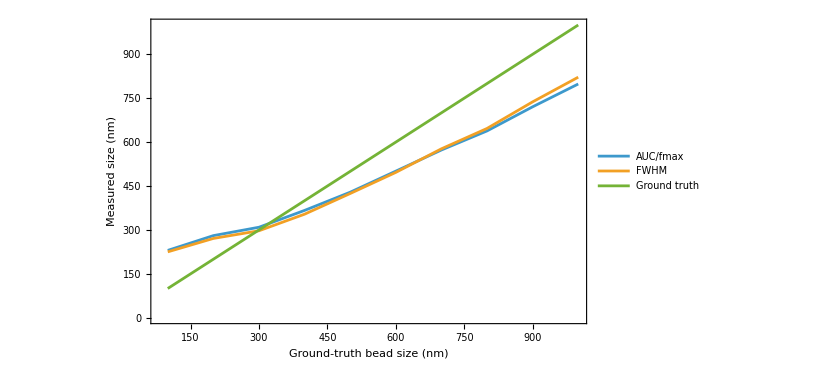
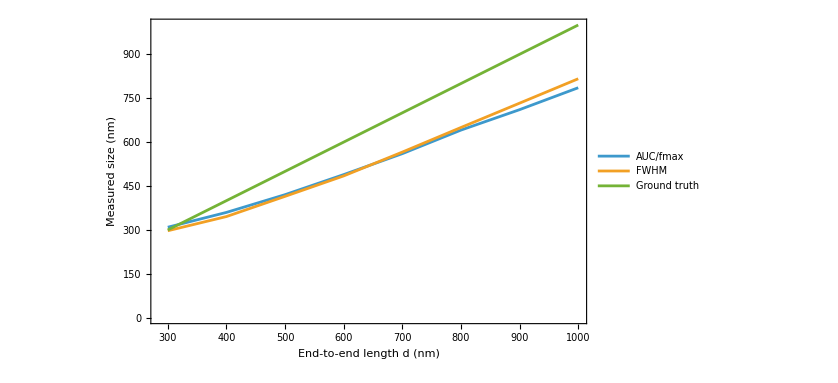
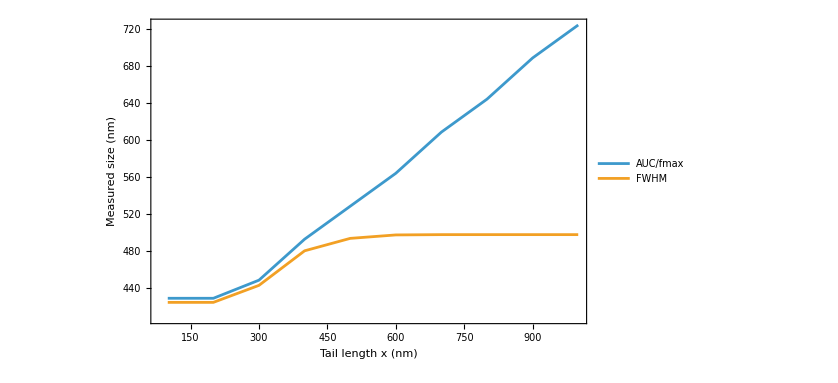
Simulated signal examples
100 nm circular bead | 300 x 700 nm oval signal | 500 nm core with 500 nm tail
-Graphics- | -Graphics- | -Graphics-
Circular bead benchmark
-Graphics-
Oval signal benchmark
-Graphics-
Tail signal benchmark
-Graphics-
Measurement table

```mathematica
(*Use the PSF coefficient estimated from the bead calibration section.*)
psfCoefficient=recommendedPsfCoefficient;

(*Simulation window for the synthetic object images.*)
simulationHalfWindowPixels=100;

(*Keep the original PSF support size.Values in the extreme tail are handled safely below.*)
psfHalfWindowPixels=50;

(*Subpixel sampling smooths binary object edges without changing the measurement method.*)
subpixelSamplesPerPixel=4;

coordinateRange=Range[-simulationHalfWindowPixels,simulationHalfWindowPixels];
psfCoordinateRange=Range[-psfHalfWindowPixels,psfHalfWindowPixels];

subpixelOffsets=N[(Range[subpixelSamplesPerPixel]-0.5)/subpixelSamplesPerPixel-0.5];

(*Values below this cutoff are far below any measurable contribution.Setting them to zero avoids machine-underflow warnings while preserving the result.*)
psfTailCutoff=10^-250;

safeGaussianPsfValue[x_,y_]:=Module[{exponent},exponent=psfCoefficient (x^2+y^2);
If[exponent>-Log[psfTailCutoff],0.,Exp[-exponent]]];

psfKernelMatrix=N@Table[safeGaussianPsfValue[x,y],{y,psfCoordinateRange},{x,psfCoordinateRange}];

psfKernelMatrix=psfKernelMatrix/Total[Flatten[psfKernelMatrix]];
psfKernelImage=Image[psfKernelMatrix,"Real"];

(*Estimate how much of each pixel is inside the analytical object shape.*)
samplePixelRegion[regionFunction_,xPixel_,yPixel_]:=Mean[Flatten[Table[Boole[TrueQ[regionFunction[(xPixel+dx) pixelSizeUm,(yPixel+dy) pixelSizeUm]]],{dx,subpixelOffsets},{dy,subpixelOffsets}]]];

makeMask[regionFunction_]:=N@Table[samplePixelRegion[regionFunction,xPixel,yPixel],{yPixel,coordinateRange},{xPixel,coordinateRange}];

(*Circular bead model.*)
diskMask[diameterUm_]:=makeMask[Function[{xUm,yUm},xUm^2+yUm^2<(diameterUm/2)^2]];

(*Oval signal model.The x axis is the long axis.*)
ovalMask[lengthUm_,widthUm_]:=makeMask[Function[{xUm,yUm},(xUm/(lengthUm/2))^2+(yUm/(widthUm/2))^2<1]];

(*Core plus one-sided tail model.*)
tailMask[coreDiameterUm_,tailLengthUm_,tailWidthUm_]:=makeMask[Function[{xUm,yUm},xUm^2+yUm^2<(coreDiameterUm/2)^2||(0<xUm<tailLengthUm&&-tailWidthUm/2<yUm<tailWidthUm/2)]];

(*Convolve the synthetic object with the calibrated PSF.*)
simulateSignalMatrix[maskMatrix_]:=ImageData[ImageConvolve[Image[maskMatrix,"Real"],psfKernelMatrix]];

(*Long-axis intensity profile.*)
profileAlongLength[matrix_]:=Total[matrix];

aucOverFmaxPixels[profile_]:=Module[{values,peak},values=N[profile];
peak=Max[values];
If[!NumericQ[peak]||peak<=0,Missing["NoSignal"],Total[values]/peak]];

interpolatedFwhmPixels[profile_,fraction_:0.5]:=Module[{values,peak,threshold,n,peakIndex,leftIndex,rightIndex,leftCrossing,rightCrossing,denominator},values=N[profile];
n=Length[values];
peak=Max[values];
If[!NumericQ[peak]||peak<=0,Return[Missing["NoSignal"]]];
threshold=fraction peak;
peakIndex=First[Ordering[values,-1]];
leftIndex=peakIndex;
While[leftIndex>1&&values[[leftIndex]]>=threshold,leftIndex--];
leftCrossing=If[leftIndex==1&&values[[leftIndex]]>=threshold,1,denominator=values[[leftIndex+1]]-values[[leftIndex]];
If[denominator==0,leftIndex,leftIndex+(threshold-values[[leftIndex]])/denominator]];
rightIndex=peakIndex;
While[rightIndex<n&&values[[rightIndex]]>=threshold,rightIndex++];
rightCrossing=If[rightIndex==n&&values[[rightIndex]]>=threshold,n,denominator=values[[rightIndex]]-values[[rightIndex-1]];
If[denominator==0,rightIndex,rightIndex-1+(threshold-values[[rightIndex-1]])/denominator]];
rightCrossing-leftCrossing];

toNanometers[value_]:=If[NumericQ[value],value pixelSizeUm 1000,value];

measureSignal[condition_,maskMatrix_,metadata_Association:<||>]:=Module[{signalMatrix,profile,aucPixels,fwhmPixels},signalMatrix=simulateSignalMatrix[maskMatrix];
profile=profileAlongLength[signalMatrix];
aucPixels=aucOverFmaxPixels[profile];
fwhmPixels=interpolatedFwhmPixels[profile,0.5];
Join[<|"Condition"->condition|>,metadata,<|"AUC/fmax length (nm)"->toNanometers[aucPixels],"FWHM length (nm)"->toNanometers[fwhmPixels],"Image"->ImageAdjust[Image[signalMatrix,"Real"]]|>]];

(*Circular-bead benchmark:compare the measured AUC/fmax and FWHM lengths against known bead diameters.*)
beadDiameterNmValues=Range[100,1000,100];

diskSimulationRows=Table[measureSignal["Circular bead",diskMask[diameterNm/1000],<|"Ground-truth bead size (nm)"->diameterNm|>],{diameterNm,beadDiameterNmValues}];

(*Oval-signal benchmark:keep the short-axis width fixed and vary the long-axis end-to-end length.*)
ovalWidthNm=300;
ovalLengthNmValues=Range[300,1000,100];

ovalSimulationRows=Table[measureSignal["Oval signal",ovalMask[lengthNm/1000,ovalWidthNm/1000],<|"End-to-end length d (nm)"->lengthNm,"Width (nm)"->ovalWidthNm|>],{lengthNm,ovalLengthNmValues}];

(*Tail-signal benchmark:keep the circular core and tail width fixed,then vary the one-sided tail length.*)
tailCoreDiameterNm=500;
tailWidthNm=200;
tailLengthNmValues=Range[100,1000,100];

tailSimulationRows=Table[measureSignal["Disk with tail",tailMask[tailCoreDiameterNm/1000,tailLengthNm/1000,tailWidthNm/1000],<|"Core diameter (nm)"->tailCoreDiameterNm,"Tail length x (nm)"->tailLengthNm,"Tail width (nm)"->tailWidthNm|>],{tailLengthNm,tailLengthNmValues}];

(*Combine all simulated measurements into one table-ready result list.*)
simulationRows=Join[diskSimulationRows,ovalSimulationRows,tailSimulationRows];

(*Extract numeric {x,y} pairs for plotting and ignore missing values.*)
numericSeries[rows_,xKey_,yKey_]:=Cases[({Lookup[#,xKey,Missing[]],Lookup[#,yKey,Missing[]]}&)/@rows,{x_?NumericQ,y_?NumericQ}];

(*Plot circular beads:AUC/fmax and FWHM measurements against ground truth.*)
diskBenchmarkPlot=ListLinePlot[{numericSeries[diskSimulationRows,"Ground-truth bead size (nm)","AUC/fmax length (nm)"],numericSeries[diskSimulationRows,"Ground-truth bead size (nm)","FWHM length (nm)"],({#,#}&)/@beadDiameterNmValues},PlotLegends->{"AUC/fmax","FWHM","Ground truth"},Frame->True,Axes->False,FrameLabel->{"Ground-truth bead size (nm)","Measured size (nm)"},PlotRange->All,ImageSize->620];

(*Plot oval signals:measured length versus known end-to-end long-axis length.*)
ovalBenchmarkPlot=ListLinePlot[{numericSeries[ovalSimulationRows,"End-to-end length d (nm)","AUC/fmax length (nm)"],numericSeries[ovalSimulationRows,"End-to-end length d (nm)","FWHM length (nm)"],({#,#}&)/@ovalLengthNmValues},PlotLegends->{"AUC/fmax","FWHM","Ground truth"},Frame->True,Axes->False,FrameLabel->{"End-to-end length d (nm)","Measured size (nm)"},PlotRange->All,ImageSize->620];

(*Plot tail signals:this shows how each metric responds as dim asymmetric signal is added to one side.*)
tailBenchmarkPlot=ListLinePlot[{numericSeries[tailSimulationRows,"Tail length x (nm)","AUC/fmax length (nm)"],numericSeries[tailSimulationRows,"Tail length x (nm)","FWHM length (nm)"]},PlotLegends->{"AUC/fmax","FWHM"},Frame->True,Axes->False,FrameLabel->{"Tail length x (nm)","Measured size (nm)"},PlotRange->All,ImageSize->620];

(*Keep a consistent column order for the displayed measurement table.*)
measurementColumns={"Condition","Ground-truth bead size (nm)","End-to-end length d (nm)","Width (nm)","Core diameter (nm)","Tail length x (nm)","Tail width (nm)","AUC/fmax length (nm)","FWHM length (nm)"};

(*Convert associations into a compact Dataset for review and export if needed.*)
simulationMeasurementTable=Dataset[AssociationThread[measurementColumns,Lookup[#,measurementColumns,Missing["NotApplicable"]]]&/@simulationRows];

(*Representative simulated images for visual inspection.*)
diskExampleImage=ImageResize[diskSimulationRows[[1,"Image"]],160];

ovalExampleImage=ImageResize[FirstCase[ovalSimulationRows,row_Association/;row["End-to-end length d (nm)"]==700:>row["Image"]],160];

tailExampleImage=ImageResize[FirstCase[tailSimulationRows,row_Association/;row["Tail length x (nm)"]==500:>row["Image"]],160];

(*Final notebook display:examples,benchmark plots,and the measurement table.*)
Column[{Style["Simulated signal examples",14,Bold],Grid[{{Style["100 nm circular bead",Bold],Style["300 x 700 nm oval signal",Bold],Style["500 nm core with 500 nm tail",Bold]},{diskExampleImage,ovalExampleImage,tailExampleImage}},Spacings->{2,1}],Style["Circular bead benchmark",14,Bold],diskBenchmarkPlot,Style["Oval signal benchmark",14,Bold],ovalBenchmarkPlot,Style["Tail signal benchmark",14,Bold],tailBenchmarkPlot,Style["Measurement table",14,Bold],simulationMeasurementTable},Spacings->1.2]
```